```mathematica
path = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Aula9_0310/Results/";
data = Import[path <> "ManySprings.txt", "Data"];
n = (Length@data[[1]]-1)/2;
Manipulate[ListPlot[{1+data[[i]][[2*#]], 1} &/@Range[n], PlotStyle -> PointSize[0.05], PlotRange->{{0,n+2},{0,2}}] , {i, 1,Length@data,1}]
```

```mathematica
x = {data[[All,{1,2}]], data[[All,{1,4}]], data[[All,{1,6}]]};
v = {data[[All,{1,3}]], data[[All,{1,5}]], data[[All,{1,7}]]};
ListLinePlot[x]
ListLinePlot[v]
```

-Graphics-

-Graphics-

```mathematica
(*Scherer*)
((#-1)/4//N)&/@Range[1,10]
```

{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25}

```mathematica
a = Min[11/4,8/3];
n= ((#-1)/4//N)&/@Range[1,10]
(a (4.0(n[[#]]-Floor[n[[#]]])+0.5))&/@Range[1,10,1]
```

{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25}

{1.33333,4.,6.66667,9.33333,1.33333,4.,6.66667,9.33333,1.33333,4.}

```mathematica
(a ( Ceiling[#/4.0]-0.5))&/@Range[1,10,1]
```

{1.33333,1.33333,1.33333,1.33333,4.,4.,4.,4.,6.66667,6.66667}

```mathematica
Plot[{{Sin[2π x],{x,-0,1}}}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

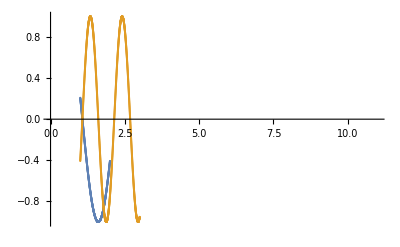

```mathematica
(*Plot[Piecewise[{{0.1 Sin[4π x],1<x<2},{0.1 Sin[2π x],2<x<3},{0.1 Sin[8π x],3<x<4}}],{x,0,5}]*)
(*ListPlot[Table[{#,Sin[2π #/(i/2)]}&/@Range[1,i ,0.001],{i,{2,3}}],PlotRange->{{0,5},{-1,1}}]*)
(*Manipulate[ListPlot[{#,Sin[#]}&/@Range[1,a,0.001],PlotRange->{{0,11},{-1,1}}],{a,2,10,1}]*)
ListPlot[{{#,Sin[14π#/15]}&/@Range[1,2,0.001],{#,Sin[28π#/15]}&/@Range[1,3,0.001]},PlotRange->{{0,11},{-1,1}}]
```

```mathematica
Range[1,2 ,0.1]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
{#,Sin[#/2]}&/@Range[1,2]
```

{{1,Sin[1/2]},{2,Sin[1]}}